```mathematica
Clear["Global`*"]
```

# DE Remainder 2

## Cory Aitchison - February 2022

Plot the remainder for the Long data

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param  /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
flatests = {A->0.242423,B->0.898534};
taylorests[0] = {A->0.033327514775158475,B->1.153359200278144};
taylorests[1] = {A->0.24242264239512362,B->0.8985343791605391};
taylorests[3] = {A->0.33494186742400267,B->0.6945601303275413};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

### Long data

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
data4 = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/4thOrderDispersion.csv"];
```

```mathematica
fdata = Interpolation[data];
```

### Differentiation

```mathematica
FD[f_, n_]:=InverseFourierTransform[FourierTransform[f[x], x, w] (I w)^n, w, x];
```

```mathematica
NFD[tdat_, ydat_, n_?IntegerQ]:=Module[{num, range, δt, δω, nydata},
num = Length[tdat];
range = Max[tdat] - Min[tdat];
δt = range / num // N;
δω = (2 Pi)/(num δt)// N;
time = Table[(j -(num/2))*δt, {j, 1, num}];
freq = Table[(j-(num/2))*δω, {j, 1, num}];
nydata = RotateLeft[data[[;;,2]], num/2-1];
fωdata = Chop[RotateRight[Fourier[nydata], num/2-1]];
nydata = RotateLeft[Table[fωdata[[j]] (I freq[[j]])^n, {j,1,num}], num/2-1];
ft2data = Chop[RotateRight[InverseFourier[nydata], num/2-1]];
 Abs[ft2data]
];
```

```mathematica
FiniteDifference[dat_]:=Transpose[{MovingMap[#[[241]]&,dat[[;;,1]],480],MovingMap[(7 (#[[1]]+ #[[481]]) -  96(#[[61]]+#[[421]]) + 676(#[[121]]+#[[361]]) - 1952(#[[181]]+#[[301]]) + 2730#[[241]])/240&, dat[[;;,2]], 480] / MovingMap[(#[[241]]-#[[240]])^4&, dat[[;;,1]], 480]}];
```

## Long data

### Long’s Answer

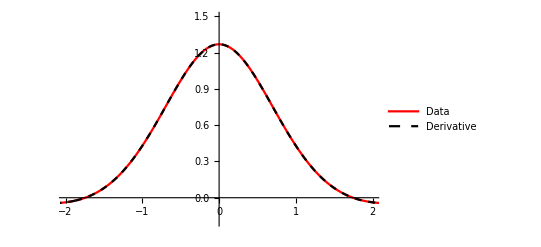

```mathematica
ListLinePlot[{data, data4}, PlotRange->{{-2,2}, {-0.2,1.5}}, PlotStyle-> {{Red, Thick}, {Black, Dashed, Thick}}, PlotLegends->{Data, Derivative}]
```

### My attempt

It is too noisy to take derivatives the normal way

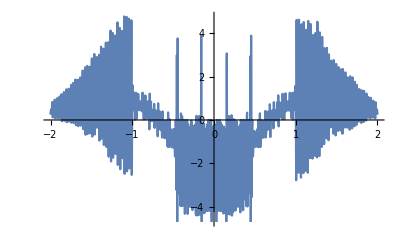

```mathematica
Plot[fdata''[x],{x,-2,2}]
```

## Discrete Fourier Transform Example

```mathematica
num = 2^12;
range = 400;
δt = range / num // N;
δω = (2 Pi)/(num δt)// N;
time = Table[(j -(num/2))*δt, {j, 1, num}];
freq = Table[(j-(num/2))*δω, {j, 1, num}];
```

```mathematica
f[t_]=Cos[t];
```

```mathematica
ftdata = Table[f[time[[j]]],{j,1,num}];
nydata = RotateLeft[ftdata, num/2-1];
fωdata = Chop[RotateRight[Fourier[nydata], num/2-1]];
```

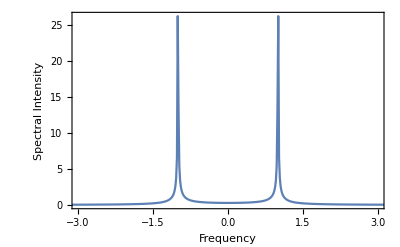

```mathematica
ListLinePlot[Table[{freq[[j]], Abs[fωdata[[j]]]}, {j,1,num}], PlotRange->{{-3,3},All}, Frame -> True, FrameLabel-> {"Frequency", "Spectral Intensity"}]
```

```mathematica
nydata = RotateLeft[Table[fωdata[[j]] freq[[j]]^4, {j,1,num}], num/2-1];
ft2data = Chop[RotateRight[InverseFourier[nydata], num/2-1]];
```

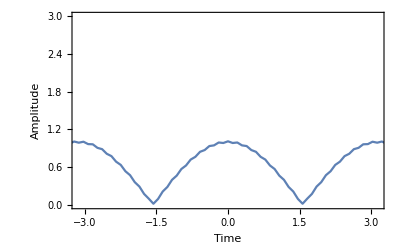

```mathematica
ListLinePlot[Table[{time[[j]], Abs[ft2data[[j]]]}, {j,1,num}], PlotRange->{{-Pi, Pi},{0, 3}}, Frame -> True, FrameLabel-> {"Time", "Amplitude"}]
```

## Long data with discrete Fourier differentiation

```mathematica
num = Length[data[[;;,1]]];
range = 160;
δt = range / num // N;
δω = (2 Pi)/(num δt)// N;
time = Table[(j -(num/2))*δt, {j, 1, num}];
freq = Table[(j-(num/2))*δω, {j, 1, num}];
```

```mathematica
nydata = RotateLeft[data[[;;,2]], num/2-1];
fωdata = Chop[RotateRight[Fourier[nydata], num/2-1]];
```

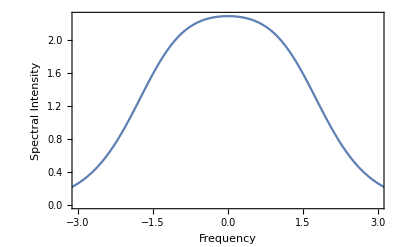

```mathematica
ListLinePlot[Table[{freq[[j]], Abs[fωdata[[j]]]}, {j,1,num}], PlotRange->{{-3,3},All}, Frame -> True, FrameLabel-> {"Frequency", "Spectral Intensity"}]
```

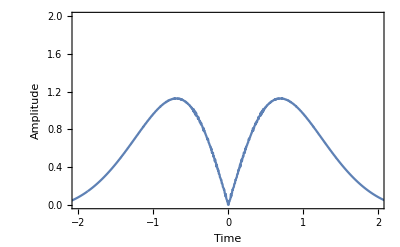

```mathematica
nydata = RotateLeft[Table[fωdata[[j]] freq[[j]], {j,1,num}], num/2-1];
ft2data = Chop[RotateRight[InverseFourier[nydata], num/2-1]];
ListLinePlot[Table[{time[[j]], Abs[ft2data[[j]]]}, {j,1,num}], PlotRange->{{-2,2},{0,2}}, Frame -> True, FrameLabel-> {"Time", "Amplitude"}]
```

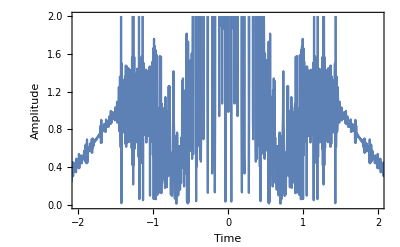

```mathematica
nydata = RotateLeft[Table[fωdata[[j]] freq[[j]]^2, {j,1,num}], num/2-1];
ft2data = Chop[RotateRight[InverseFourier[nydata], num/2-1]];
ListLinePlot[Table[{time[[j]], Abs[ft2data[[j]]]}, {j,1,num}], PlotRange->{{-2,2},{0,2}}, Frame -> True, FrameLabel-> {"Time", "Amplitude"}]
```

### Function

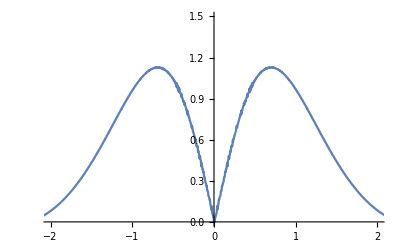

```mathematica
y = NFD[data[[;;,1]], data[[;;,2]], 1];
ListLinePlot[Transpose[{time, y}], PlotRange->{{-2,2},{0,1.5}}]
```

This is still too noisy

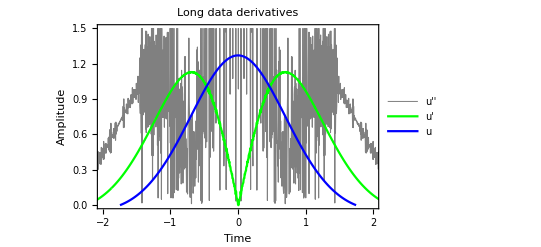

```mathematica
ListLinePlot[{Transpose[{time, NFD[data[[;;,1]], data[[;;,2]], 2]}], Transpose[{time, NFD[data[[;;,1]], data[[;;,2]], 1]}], data}, PlotRange->{{-2,2},{0,1.5}}, PlotStyle->{{Gray, Thickness[0.002]}, {Green, Thick}, {Blue, Thick}}, PlotLegends->{"u''", "u'", "u"}, Frame -> True, FrameLabel->{"Time", "Amplitude"}, PlotLabel->"Long data derivatives"]
```

Perhaps if we only take one every 8/16 data points?

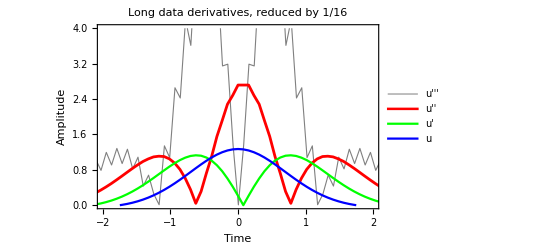

```mathematica
Block[{data = Take[data, {1,-1,16}], time = Take[time, {1,-1,16}]},ListLinePlot[{Transpose[{time, NFD[data[[;;,1]], data[[;;,2]], 3]}],Transpose[{time, NFD[data[[;;,1]], data[[;;,2]], 2]}], Transpose[{time, NFD[data[[;;,1]], data[[;;,2]], 1]}], data}, PlotRange->{{-2,2},{0,4}}, PlotStyle->{{Gray, Thickness[0.002]}, {Red, Thickness[0.005]}, {Green, Thick}, {Blue, Thick}}, PlotLegends->{"u'''", "u''", "u'", "u"}, Frame -> True, FrameLabel->{"Time", "Amplitude"}, PlotLabel->"Long data derivatives, reduced by 1/16"]]
```

## Long data with finite difference

```mathematica
fddata = Block[{data =Select[data, Abs[#[[1]]] <=25&]}, FiniteDifference[data]];
```

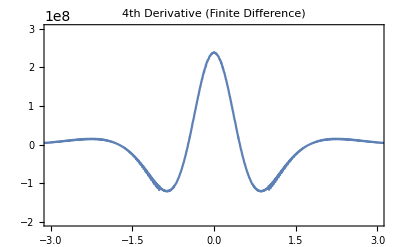

```mathematica
ListLinePlot[fddata, PlotRange->{{-3,3},{-2*^8, 3*^8}}, Frame->True, PlotLabel->"4th Derivative (Finite Difference)"]
```

## Contributions

What are the contributions from the three components of the DE?

```mathematica
de1[f_]:=x|->(D[f[t], {t,4}] /. t->x);
de2[f_]:=x |-> 4 σ^4 f[x];
de3[f_]:=x|-> Γ f[x]^3;
```

```mathematica
de1fddata = Interpolation[fddata];
```

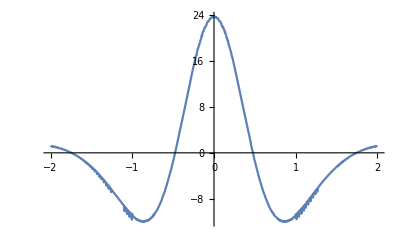

```mathematica
Plot[de1fddata[x]*1*^-7,{x,-2,2}]
```

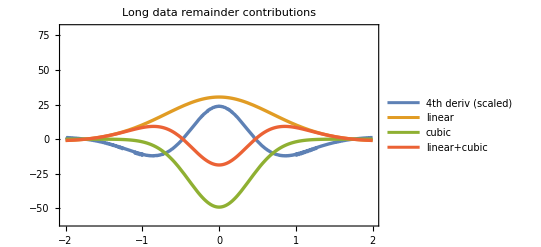

```mathematica
Plot[{
de1fddata[x]/1*^7,
de2[fdata][x] /. param /. estimates,
de3[fdata][x] /. param /. estimates,
de2[fdata][x] + de3[fdata][x] /. param /. estimates
}, {x,-2,2},PlotLegends-> {"4th deriv (scaled)", "linear", "cubic","linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}, PlotLabel->"Long data remainder contributions", Frame->True]
```

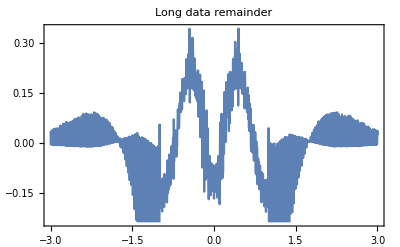

```mathematica
Plot[de1fddata[x]*0.78*^-7 + de2[fdata][x] + de3[fdata][x] /. param /. estimates, {x,-3,3}, Frame -> True, PlotLabel->"Long data remainder"]
```